```mathematica
numbers={a->1.,ν->0.07453,α->0.000002};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом\Diploma_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, 1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
DataList[x_]:=Transpose[{FreqList[x][[NumPlace[x]-3;;NumPlace[x]+3]],AbsFourier[x][[NumPlace[x]-3;;NumPlace[x]+3]]}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

N = 1500

0.0746667

{{0.0726667,0.000318944},{0.0733333,0.0147087},{0.074,0.0712158},{0.0746667,0.0992632},{0.0753333,0.0441421},{0.076,0.00487991},{0.0766667,0.000433379}}

{{0.0726667,0.00281405},{0.0733333,0.0185712},{0.074,0.0685725},{0.0746667,0.0909307},{0.0753333,0.0458059},{0.076,0.00824051},{0.0766667,0.00160282}}

{{0.0726667,0.0297791},{0.0733333,0.0491229},{0.074,0.132027},{0.0746667,0.201666},{0.0753333,0.0823604},{0.076,0.0375269},{0.0766667,0.024935}}

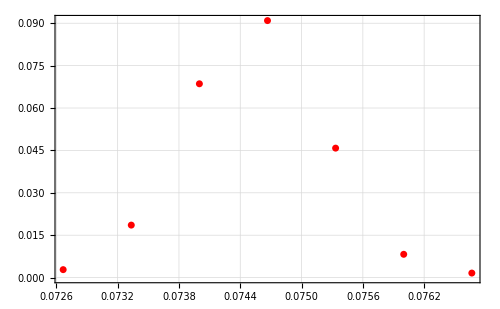

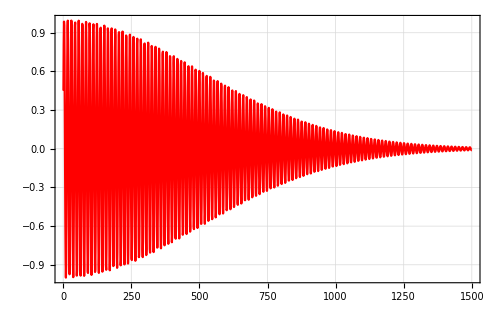

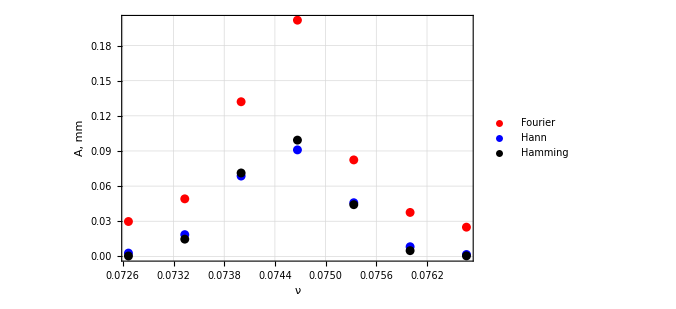

Windows1500.png

```mathematica
Hann1500=Table[Sin[(k π)/1499.]^2*a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,1500}];
Hamming1500=Table[(0.53836-0.46164Cos[(2Pi*k)/1499])a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,1500}];
sig1500=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,1500}];

Freq1500 =Freq[sig1500]
DataSetHamming=DataList[Hamming1500]
DataSetHann=DataList[Hann1500]
DataSetSig=DataList[sig1500]
ListPlot[DataSetHann]
Image1500=ListLinePlot[sig1500]
Windows1500=ListPlot[{Legended[DataSetSig,"Fourier"],Legended[DataSetHann,"Hann"],Legended[DataSetHamming,"Hamming"]},FrameLabel->{"ν","A, mm"},PlotStyle->{Red,Blue,Black}]
Export["Windows1500.png",Windows1500]
```